## mois

```mathematica
irrotational[k_,beta_,gamma_]:=Sin[gamma*π/180-2π/3*k]^2;
rigid[k_,beta_,gamma_]:=1-Sqrt[5/(4π)]beta*Cos[gamma*π/180-2π/3*k];
```

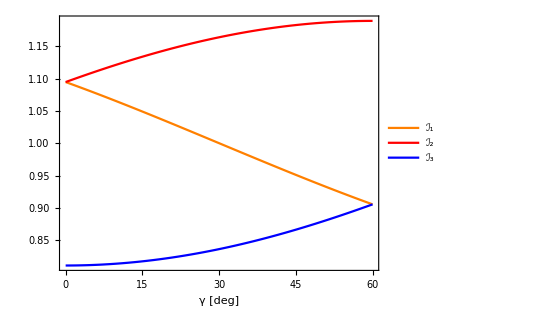

```mathematica
p1=Plot[{rigid[1,0.3,x],rigid[2,0.3,x],rigid[3,0.3,x]},{x,0,60},AspectRatio->0.8,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{{Orange,Thick},{Red,Thick},{Blue,Thick}},PlotLegends->{"ℐ_1","ℐ_2","ℐ_3"},LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"γ [deg]",""}];
Show[p1]
```

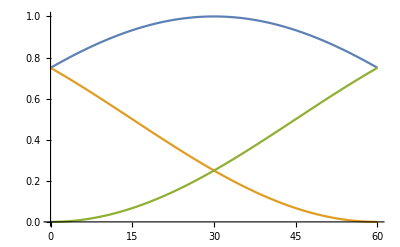

```mathematica
Plot[{irrotational[1,0.3,x],irrotational[2,0.3,x],irrotational[3,0.3,x]},{x,0,60}]
```